Set::write: Tag Times in Keplar (potential:a) is Protected.

1.

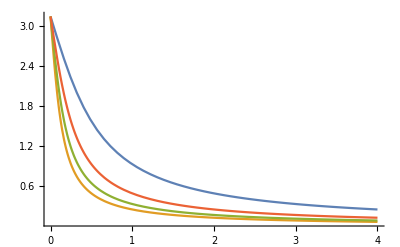

```mathematica
Keplar potential :
 a=1.0
Remove[s,a]
 f1[s_,Ep_]:=2*ArcCot[2*Ep*s]
  Plot[{f1[s,1],f1[s,4],f1[s,3],f1[s,2]},{s,0,4},PlotRange->All]
```

```mathematica
f2[p_,Ep_]:=1/(16*Ep^2)(Csc[p/2])^4
```

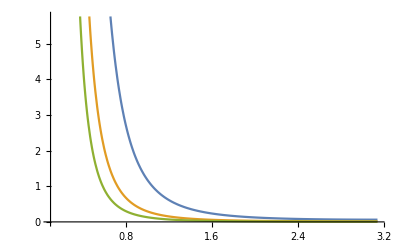

```mathematica
Plot[{f2[p,1],f2[p,2],f2[p,3]},{p,0.1,Pi}]
```

```mathematica
Hard sphere potential:
```

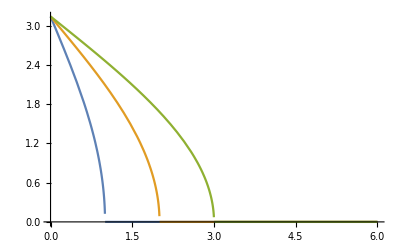

```mathematica
f4[R_,q_]:=Piecewise[{{2ArcCos[q/R],0≤ q≤R},{0,q>R}}]

Plot[{f4[1,q],f4[2,q],f4[3,q]},{q,0,6}]
```

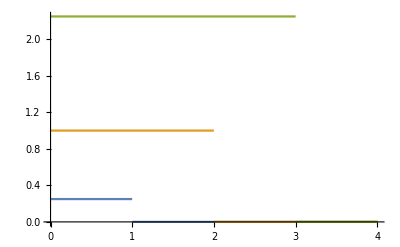

```mathematica
f3[R_,r_]:=Piecewise[{{R^2/4,0≤ r≤R}}]

Plot[{f3[1,r],f3[2,r],f3[3,r]},{r,0,4}]
```

Sum of attractive and repulsive potential :

```mathematica
s={u''[t]+u[t]-2.3(u[t])^2+(u[t])^3==0}
ics= {u[0]==1,u'[0]==0.5}
sol=Solve[{s},{u}]
sol=NDSolve[{s,ics},{u},{t,-200,200}]

PolarPlot[Evaluate[1/u[t]/.sol],{t,0,200}]
```

{u[t]-2.3 u[t]^2+u[t]^3+u''[t]==0}

{u[0]==1,u'[0]==0.5}

Solve::naqs: {u[t]-2.3 u[t]^2+u[t]^3+u''[t]==0} is not a quantified system of equations and inequalities.

Solve[{{u[t]-2.3 u[t]^2+u[t]^3+u''[t]==0}},{u}]

```mathematica
{{u->InterpolatingFunction[…]}}
Orbit for this potential:
```

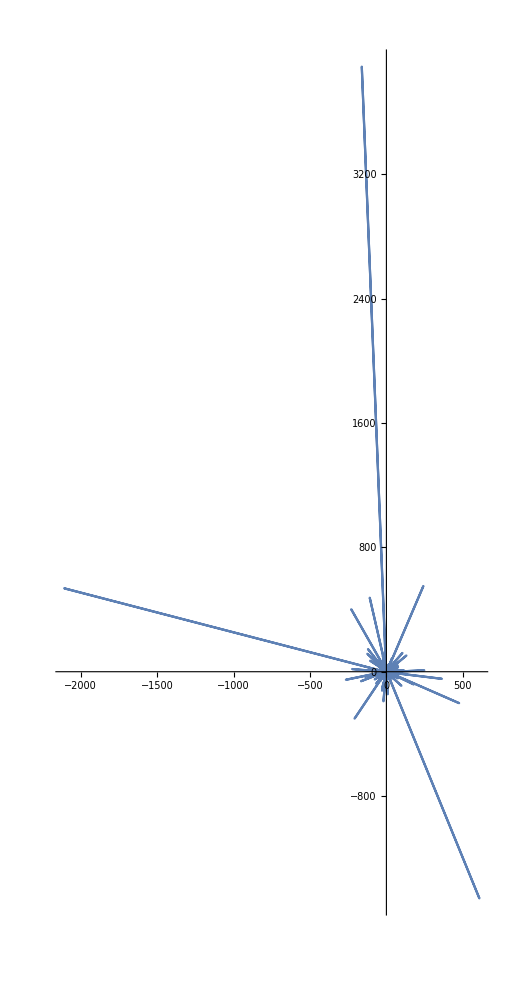

```mathematica
Here we have to evaluate the integral :
Θ(E)  =   π-2  Subscript[(∫l/(√(2mE))*1/r^2*1/(√(2 mE/l^2-(2m)/l^2(b/r^4-a/r^3)-1/r^2))ⅆr), Subscript[r, m]]^∞

For which the computer has stopped working while running.  But this is the form to evaluate the scattering angle w.r.t  E.  With that form we have to evaluate the cross section (dσ/(d(cosΘ))).
```